```mathematica
min=.1
max=1
```

0.1

1

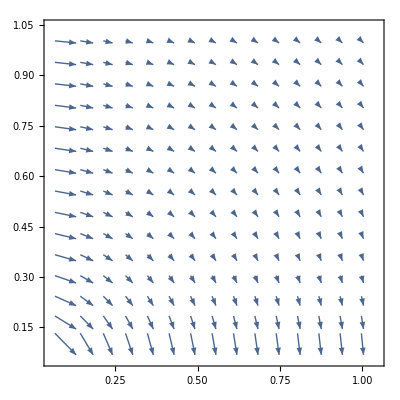

```mathematica
VectorPlot[{1/(2x),-1/(2y)},{x,min,max},{y,min,max}]
```

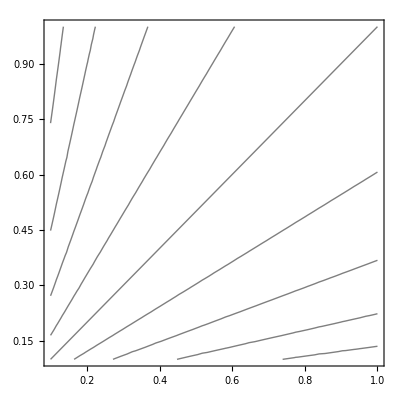

```mathematica
ContourPlot[Log[x/y]/2,{x,min,max},{y,min,max},ContourStyle->Black,ContourShading->None]
```

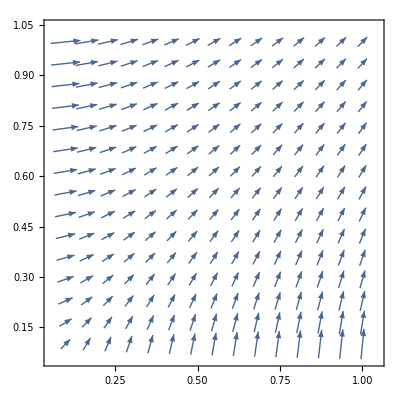

```mathematica
VectorPlot[{y/(2Sqrt[x y]),x/(2Sqrt[x y])},{x,min,max},{y,min,max}]
```

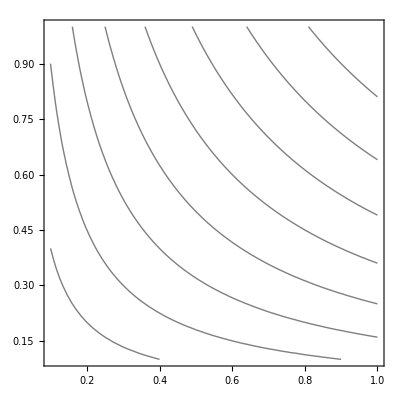

```mathematica
ContourPlot[Sqrt[x y],{x,min,max},{y,min,max},ContourStyle->Black,ContourShading->None]
```

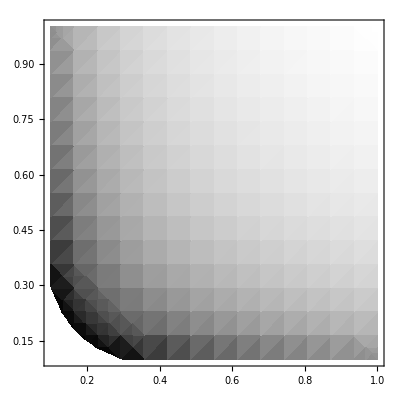

```mathematica
DensityPlot[-1/(2Sqrt[x y]),{x,min,max},{y,min,max},ColorFunction->GrayLevel]
```

```mathematica
?DensityPlot
```

DensityPlot[f,{x,x_min,x_max},{y,y_min,y_max}] makes a density plot of f as a function of x and y.